```mathematica
Quit[]
```

```mathematica
<<Toolbox`
<<Toolbox`Style`
SetDirectory[NotebookDirectory[]];

enzModelsDir = "/home/mrama/Dropbox/MASSef/examples/"
mainDir=enzModelsDir<>"code_data/";
Import[mainDir<>"sim_plot_functions.m"];
Import[mainDir<>"simulation.m"];
```

/home/mrama/Dropbox/MASSef/examples/

## Build models

```mathematica
baseDir =enzModelsDir<> "TPI/fit_TPI/output/";
(*eqParams = Import[baseDir <> "treated_data/predicted_params_distribution_pedRevParams_p10_2_log_ssd.csv", "CSV"];
eMASSModelList=Import[baseDir<>"model_simulations/models/model_TPI_all_2.mx"];*)
eqParams = Import[baseDir <> "treated_data/predicted_params_distribution_predRevParams_p10_10000_1_log_ssd.csv", "CSV"];
eMASSModelList=Import[baseDir<>"model_simulations/models/model_TPI_all_10000_1.mx"];
```

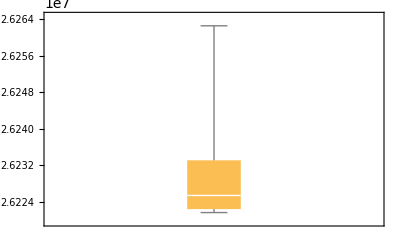

```mathematica
BoxWhiskerChart[eqParams[[3;;68,3]]/eqParams[[3;;68,2]]]
```

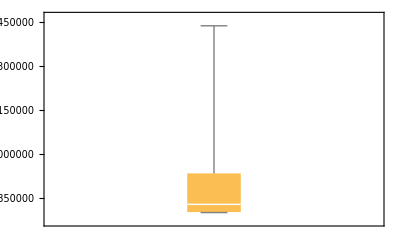

```mathematica
BoxWhiskerChart[eqParams[[3;;68,6]]/eqParams[[3;;68,5]]]
```

```mathematica
ssdThreshold=0.1;
baseModel=constructModel[{Overscript[g3p^c⇌dhap^c, TPI]}];
updateCustomRateLaws[baseModel, {Subscript[v, TPI]->(((TPI^)_^ Underscript[kcat_f, FBP2] g3p^c[t])/Km_g3p^-((TPI^)_^ Underscript[kcat_r, FBP2] dhap^c[t])/Km_dhap^)/(1+g3p^c[t]/Km_g3p^+dhap^c[t]/Km_dhap^)}];
(*updateCustomRateLaws[baseModel, {Subscript[v, TPI]->(((TPI^)_^ kcat_f_FBP2)/Km_g3p^(g3p^c[t]-dhap^c[t]/K_TPI))/(1+g3p^c[t]/Km_g3p^+dhap^c[t]/Km_dhap^)}];*)
```

```mathematica
eqParams[[1;;5]]//TableForm
```

ssd | Km_g3p | kcat_f | Keq | Km_dhap | kcat_r
0 | 0.00103 | 27025.3 | 9.35 | 1 | 1
5.45428×10^-7 | 0.00102948 | 27025.3 | 9.34961 | 0.176788 | 602356.
5.47758×10^-7 | 0.00102938 | 27025.3 | 9.35 | 0.130013 | 419188.
5.55582×10^-7 | 0.0010296 | 27025.3 | 9.34956 | 0.000166282 | 466.426

```mathematica
modelList={};
Do[
If[eqParams[[modelI,1]]< ssdThreshold && modelI < (Length@eMASSModelList+3),

model = baseModel;

metInitialConc = FilterRules[eMASSModelList[[modelI-2]]["InitialConditions"],baseModel["Species"]];
metInitialConc=Map[Keys@# -> Values@#&, metInitialConc];
updateInitialConditions[model,metInitialConc];

paramList={ Km_g3p^-> eqParams[[modelI,2]],Underscript[kcat_f, FBP2]->eqParams[[modelI,3]], Underscript[K, TPI]-> eqParams[[modelI,4]],Km_dhap^-> eqParams[[modelI,5]], Underscript[kcat_r, FBP2]-> eqParams[[modelI,6]],  Underscript[Volume, c]-> 1, (TPI^)_^->3.86*10^-6 };
updateParameters[model, paramList];

AppendTo[modelList,model],

Break[]],

{modelI, 3,Length@eqParams}];
```

```mathematica
Length@modelList
```

6981

```mathematica
metInitialConc
```

{dhap^c→0.00305999,g3p^c→0.000270225}

```mathematica
modelList[[2]]["InitialConditions"]
```

{dhap^c→0.00305692,g3p^c→0.000271}

```mathematica
inputDir = baseDir<>"model_simulations/models/";
If[!DirectoryQ[inputDir],
	CreateDirectory[inputDir,CreateIntermediateDirectories-> True]
];
```

```mathematica
Export[inputDir<>"model_TPI_MM_rev_10000_1.mx",modelList, "MX"];
```

## MM simulations

```mathematica
getFirstMMModelData[modelI_, resWorking_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_, indMet_, tValues_]:=
	Block[{simConcEnz, simConcMets, simFlux},

	simConcMets=Join[{Flatten@{"t", headerConcMets}},
					Table[
						Flatten[{tVal, Flatten@{Values@{resWorking[[modelI, 1]][[indMet]]}} /. t-> tVal}], 
					{tVal,tValues}]];
		
	simFlux=Join[{Flatten@{"t", headerFlux}},
				Table[
					Flatten[{tVal, Flatten@{Values@resWorking[[modelI, 2]]} /. t-> tVal}], 
				{tVal,tValues}]];

	Return[{{}, simConcMets, simFlux}];
];
```

```mathematica
getMMModelData[modelI_, resWorking_, simConcEnz_, simConcMets_, simFlux_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_,  indMet_, tValues_]:=
	Block[{simConcEnzLocal, simConcMetsLocal, simFluxLocal, simConcEnzTemp, simConcMetsTemp, simFluxTemp},

						
	simConcMetsTemp=Join[{Flatten@{"t",headerConcMets}},
						Table[
							Flatten[{tVal, Flatten@{Values@{resWorking[[modelI, 1]][[indMet]]}}/.t-> tVal}],
						{tVal,tValues}]];
	
	simFluxTemp=Join[{Flatten@{"t",headerFlux}},
					Table[
						Flatten[{tVal,Flatten@{Values@resWorking[[modelI, 2]]}/.t-> tVal}],
					{tVal,tValues}]];
	
	
	simConcMetsLocal = MapThread[Flatten[{#1,#2}]&, {simConcMets,simConcMetsTemp}];
	simFluxLocal = MapThread[Flatten[{#1,#2}]&, {simFlux,simFluxTemp}];

	Return[{{},simConcMetsLocal, simFluxLocal}];
];
```

```mathematica
simulateMMEnsembleNoCheck[inputDir_, outputDir_, enzName_, modelID_, nModelEnsembles_, tFinal_, tValues_, 
				initCondList_, headerConcEnz_, headerConcMets_, headerFlux_, indEnz_, subInd_, prodInd_, KeqVal_:""]:=
	Block[{KeqData, prods, subs, indMet, modelList,
			metsList, res, resWorking, modelI, simConcEnz, simConcMets, simFlux, simConcEnzTemp, simConcMetsTemp, 
			simFluxTemp},
	 
	indMet = Flatten[{subInd, prodInd}];

	Do[

		modelList = Import[inputDir <> "model_" <> enzName <> "_" <> modelID <> "_" <> ToString[modelEnsembleI] <> ".mx"];
		Print[inputDir <> "model_" <> enzName <> "_" <> modelID <> "_" <> ToString[modelEnsembleI] <> ".mx"];
		res = Map[TimeConstrained[simulate[modelList[[#]], {t, 0, tFinal}, InitialConditions -> initCondList, MaxSteps-> Infinity], 30, "err"]&, Range[1, Length@modelList]];
		resWorking = Delete[res, Position[res,"err"]];	

		modelI=1;
				
		{simConcEnz, simConcMets, simFlux} = getFirstMMModelData[modelI, resWorking, headerConcEnz, headerConcMets, headerFlux, indEnz, indMet, tValues];
		
		Do[ (* go through individual models *)
			
				
			{simConcEnz, simConcMets, simFlux} = getMMModelData[modelI, resWorking, simConcEnz, simConcMets, 
							simFlux, headerConcEnz, headerConcMets, headerFlux, indEnz, indMet, tValues];,
	
		{modelI, 2, Length@resWorking}];

		Export[outputDir <> "/sim_res_conc_mets_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <>ToString[KeqVal] <> ".csv", simConcMets, "TSV"];
		Export[outputDir <> "/sim_res_flux_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <>ToString[KeqVal] <> ".csv", simFlux, "TSV"];

		Export[outputDir<> "/data_mx/sim_res_"<>modelID<>"_"<>ToString[modelEnsembleI] <> "_" <> ToString[KeqVal] <> ".mx", resWorking, "MX"];,

	{modelEnsembleI, nModelEnsembles[[1]], nModelEnsembles[[2]]}];
	
	
];
```

## Simulations

```mathematica
modelList[[1]]["Species"]
```

{dhap^c,g3p^c}

```mathematica
conc/.t-> tFinal
```

{f6p^c→0.0177194,fdp^c→3.94575×10^-7,pi^c→0.0390994}

```mathematica
{ Km_g3p^-> eqParams[[modelI,2]],Underscript[kcat_f, FBP2]->eqParams[[modelI,3]], Km_dhap^-> eqParams[[modelI,5]], Underscript[kcat_r, FBP2]-> eqParams[[modelI,6]],  Underscript[Volume, c]-> 1, (TPI^)_^->3.86*10^-6 }
```

```mathematica
ind=10;
Times@@(Values@FilterRules[modelList[[ind]]["Parameters"], {Km_dhap^,Underscript[kcat_f, FBP2]}])/(Times@@(Values@FilterRules[modelList[[ind]]["Parameters"], {Km_g3p^,Underscript[kcat_r, FBP2]}]))
```

17.841

```mathematica
(Values@FilterRules[conc/.t-> tFinal, {dhap^c}])/Values@FilterRules[conc/.t-> tFinal, {g3p^c}]
```

{9.35003}

```mathematica
modelList=Import[inputDir<>"model_TPI_MM_1.mx"];
```

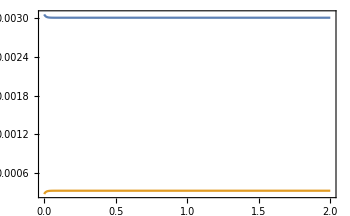

```mathematica
tFinal=2;
{conc,flux}=simulate[modelList[[80]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}, PlotFunction-> Plot]
```

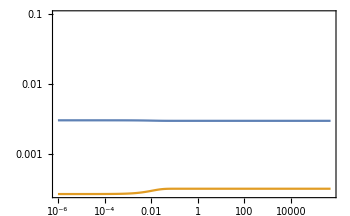

```mathematica
tFinal=5*10^5;
{conc,flux}=simulate[modelList[[2]],{t,0,tFinal}];
plotSimulation[conc,{t,0,tFinal}, PlotRange-> {{0,tFinal},{0.,0.1}}]
```

```mathematica
modelList[[2]]["Parameters"]
```

{Km_g3p^→0.00103,kcat_f_FBP2→27025.3,K_TPI→9.35,Km_dhap^→0.082897,kcat_r_FBP2→27620.7,Volume_c→1,(TPI^)_^→3.86×10^-6}

### Systematic simulations

```mathematica
enzName="TPI";

outputDirBase = baseDir<>"model_simulations/data/";
If[!DirectoryQ[outputDirBase],
	CreateDirectory[outputDirBase,CreateIntermediateDirectories-> True]
];



headerConcMets={"g3p", "dhap"};
headerFlux={"v_1"};
subInd = {2};
prodInd={1};
indEnz={};

initCondList={};
outputDirList={"noPerturb"};


tValues=Map[10^#&,Range[-6,2, 0.1]];
tFinal=100;
tValues=Insert[tValues,0., 1];


modelIDList={"MM_rev_10000"};
nModelEnsembles={1,1};


outputDir =outputDirBase;
If[!DirectoryQ[outputDir<>"/data_mx/"],
	CreateDirectory[outputDir<>"/data_mx/",CreateIntermediateDirectories-> True]
];
```

```mathematica
headerConcEnz={};
```

```mathematica
Do[

simulateMMEnsembleNoCheck[inputDir, outputDir, enzName, modelID, nModelEnsembles, tFinal, tValues, initCondList, headerConcEnz, headerConcMets, headerFlux, indEnz,subInd, prodInd];,


{modelID, modelIDList}];
```

/home/mrama/Dropbox/MASSef/examples/TPI/fit_TPI/output/model_simulations/models/model_TPI_MM_rev_10000_1.mx